# Supplemental material (File S2) for Fixation dynamics of beneficial alleles in prokaryotic polyploid chromosomes and plasmids (Santer et al., bioRxiv, 2021)

```mathematica
ClearAll["Global`*"]
$Assumptions={_∈Reals,n>1}
```

{_∈ℝ,n>1}

## Solution of x_mut(t)

```mathematica
sol=DSolve[x'[t]==-s*x[t]^2+x[t](s+a*(b*Exp[b*t])/(a*Exp[b*t]+(b-a)))&&x[0]==f,x,t]
```

{{x→Function[{t},(ⅇ^(s t) (-a+b+a ⅇ^(b t)) f (b+s))/(b^2+a b f-b^2 f-a b ⅇ^(s t) f+b^2 ⅇ^(s t) f+b s-b f s-a ⅇ^(s t) f s+b ⅇ^(s t) f s+a ⅇ^((b+s) t) f s)]}}

(There is  only a single solution (as expected).)

```mathematica
xmut[t_]=FullSimplify[x[t]/.sol[[1]]]
```

(ⅇ^(s t) (b+a (-1+ⅇ^(b t))) f (b+s))/(b (b+a f-b f+s-f s)+ⅇ^(s t) f (a ⅇ^(b t) s-(a-b) (b+s)))

Inserting a, b gives

```mathematica
ab={a->(1+s)(ξ+κ-1),b->(1+s)(ξ-1)};
```

```mathematica
xmut[t_]=FullSimplify[xmut[t]/.ab]
```

(ⅇ^(s t) f (-1+ξ+s ξ) (κ-ⅇ^((1+s) t (-1+ξ)) (-1+κ+ξ)))/((-1+ⅇ^(s t)) f κ (-1+ξ)-(-1+ξ) (-1+ξ+s ξ)+f s (-1+κ+ξ+(-1+ⅇ^(s t)) κ ξ-ⅇ^(t (-1+ξ+s ξ)) (-1+κ+ξ)))

# Decay of wild-type carrying cells x_0(t) and convergence of (x_wt(t))/(x_0(t))

Define x_hf. For large t, 1/t log x_wt(t) converges to (1+s) (-1+ξ)

```mathematica
ξκ= {ξ-> (2n-3)/(2n-1),κ->1/(2n-1)};
xhf[t_]=FullSimplify[(b*ⅇ^(b*t))/(a*ⅇ^(b*t)+b-a) /.ab]
xwt[t_]=FullSimplify[1-xmut[t]*(1-xhf[t])]
Assuming[{s>0,(1+s)ξ>1,ξ>0,ξ<1,f>0,f<1,κ<1-ξ,κ>0},Limit[1/t Log[xwt[t]],t->∞]]
```

(ⅇ^((1+s) t (-1+ξ)) (-1+ξ))/(-κ+ⅇ^((1+s) t (-1+ξ)) (-1+κ+ξ))

((-1+ξ) (-1-(-1+ⅇ^(t (-1+ξ+s ξ))) f (s (-1+κ)+κ)+ξ+s ξ))/((-1+ξ) (-1+ξ+s ξ)+f (-(-1+ⅇ^(s t)) κ (-1+ξ)+ⅇ^(t (-1+ξ+s ξ)) s (-1+κ+ξ)-s (-1+κ+ξ+(-1+ⅇ^(s t)) κ ξ)))

ConditionalExpression[(1+s) (-1+ξ),2 (1+s) ξ>2+s]

The condition 2 (1+s) ξ>2+s  must hold to obtain the analytical result (above) with MMA:

For large t, (x_wt(t))/(x_0(t)) converges to

```mathematica
Assuming[{s>0,(1+s)ξ>1,ξ>0,ξ<1,f>0,f<1,κ<1-ξ,κ>0},Limit[(1-xmut[t]*(1-xhf[t]))/(1-xmut[t]),t->∞]]
```

(s (-1+κ)+κ)/((1+s) (-1+κ+ξ))

### Convergence

The plot below shows an example for n=32 that Limit[1/t Log[xwt[t]],t→∞]equals (1+s) (-1+ξ) also if  (1+s)ξ>1 ⇔ s>1/(n-3/2) (left vertical line) holds and 2 (1+s) ξ>2+s s>2/(n-5/2) (right vertical line) is not fulfilled.

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.15,0.2,0.25,0.3}

{0.944839,0.954194,0.963548,0.972903,0.982258,0.991613,1.00097,1.01032,1.01968,1.02903,1.07581,1.12258,1.16935,1.21613}

{0.940138,0.944746,0.949309,0.953827,0.958301,0.962731,0.967119,0.971464,0.975768,0.980031,1.00075,1.02053,1.03943,1.0575}

{-0.01,-0.02,-0.03,-0.04,-0.05,-0.06,-0.0690323,-0.0696774,-0.0703226,-0.0709677,-0.0741935,-0.0774194,-0.0806452,-0.083871}

{-0.0651613,-0.0658065,-0.0664516,-0.0670968,-0.0677419,-0.0683871,-0.0690323,-0.0696774,-0.0703226,-0.0709677,-0.0741935,-0.0774194,-0.0806452,-0.083871}

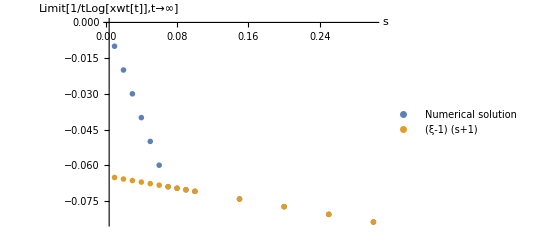

```mathematica
nrul={n->16};
slist={0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.15,0.2,0.25,0.3}
(1+slist)*ξ/.ξ-> (2n-3)/(2n-1)/.nrul
2(1+slist)/(2+slist)ξ/.ξ-> (2n-3)/(2n-1)/.nrul

y1=Table[Limit[1/t Log[xwt[t]]/.{ξ-> (2n-3)/(2n-1),κ->1/(2n-1),f->0.01}/.nrul,t->∞],{s,slist}]
y2=Table[(1+s)(-1+ξ)/.ξ-> (2n-3)/(2n-1)/.nrul,{s,slist}]
ListPlot[{Transpose[{slist,y1}],Transpose[{slist,y2}]},
PlotMarkers->"OpenMarkers",
GridLines->{{2/(n-5/2)/.nrul,1/(n-3/2)/.nrul},{0,0}}, AxesLabel->{s,"Limit[1/tLog[xwt[t]],t→∞]"},PlotRange->Full,
PlotLegends->{"Numerical solution",(1+s) (-1+ξ)}]
```

### Computation of the heterozygosity window

```mathematica
Hw[n_,s_]=Simplify[(-Log[(s (-1+κ)+κ)/((1+s) (-1+κ+ξ))])/((1+s)(ξ-1))/.ξ-> (2n-3)/(2n-1)/.κ->1/(2n-1)]
```

((-1+2 n) Log[(-1+2 (-1+n) s)/(1+s)])/(2 (1+s))

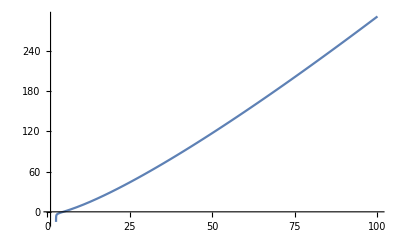

```mathematica
Plot[Hw[n,0.3],{n,1,100}]
```